# Swanepoel Step By Step

## 1. Read data and recognize max and min points

It was used another algorithm to read data and recognize maximum and minimun, here the data are presented:

```mathematica
DataMax={{534,0.26565},{562,0.54786},{600,0.79619},{649,0.89425},{709,0.91328},{788,0.91412},{891,0.91469},{1033,0.91523}}
DataMin={{537,0.26442},{577,0.41151},{622,0.48360},{677,0.51017},{746,0.52063},{836,0.52873},{955,0.53549}}
```

{{534,0.26565},{562,0.54786},{600,0.79619},{649,0.89425},{709,0.91328},{788,0.91412},{891,0.91469},{1033,0.91523}}

{{537,0.26442},{577,0.41151},{622,0.4836},{677,0.51017},{746,0.52063},{836,0.52873},{955,0.53549}}

## 2. Calculate envelopments (3 Point Parabolic Interpolation of data)

As recommended in the paper of Swanepoel’s method, a 3 point interpolation must be made in order to obtain the envelope values for max and min transmitances, there mus not be used any mathematical model since it could increase the risk of error, as well as a interpolation for the whloe points of an envelope is very unnacurate as shown:

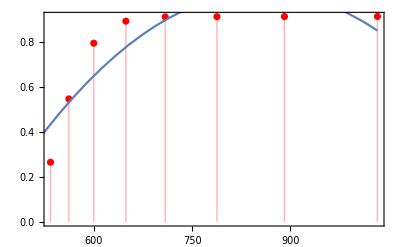

```mathematica
DataMax={{534,0.26565},{562,0.54786},{600,0.79619},{649,0.89425},{709,0.91328},{788,0.91412},{891,0.91469},{1033,0.91523}};
lm = LinearModelFit[DataMax, {x^2,x}, x];
Show[ListPlot[DataMax, PlotStyle -> Red,Filling->Bottom],Plot[lm[x],{x, 0, 1033}],Frame -> True]
```

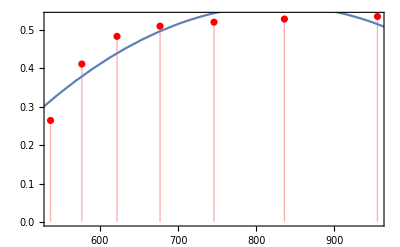

```mathematica
DataMin={{537,0.26442},{577,0.41151},{622,0.48360},{677,0.51017},{746,0.52063},{836,0.52873},{955,0.53549}};
LM = LinearModelFit[DataMin, {x^2,x}, x];
Show[ListPlot[DataMin, PlotStyle -> Red,Filling->Bottom],Plot[LM[x],{x, 0, 1033}],Frame -> True]
```

There is no polinomyal interpolation that fits correctly the given data, so it is needed to perform parabolic interpolation between three succesive point for the maxima and the minima, as well as calculate the corresponding transmitance for each extrema.

## Maximum points for inferior transmitances

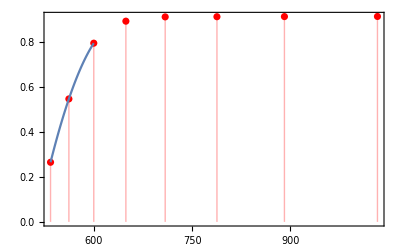

0.299914

0.66441

```mathematica
lm1 = LinearModelFit[{{534,0.26565},{562,0.54786},{600,0.79619}}, {x^2,x}, x];
Show[ListPlot[DataMax, PlotStyle -> Red,Filling->Bottom],Plot[lm1[x],{x, 534, 600}],Frame -> True]
lm1[537]
lm1[577]
```

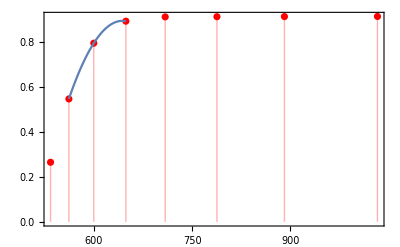

0.663864

0.871172

```mathematica
lm2 = LinearModelFit[{{562,0.54786},{600,0.79619},{649,0.89425}}, {x^2,x}, x];
Show[ListPlot[DataMax, PlotStyle -> Red,Filling->Bottom],Plot[lm2[x],{x, 562, 649}],Frame -> True]
lm2[577]
lm2[622]
```

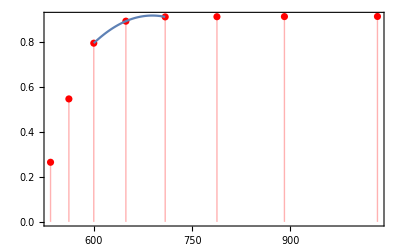

0.849394

0.916974

```mathematica
lm3 = LinearModelFit[{{600,0.79619},{649,0.89425},{709,0.91328}}, {x^2,x}, x];
Show[ListPlot[DataMax, PlotStyle -> Red,Filling->Bottom],Plot[lm3[x],{x, 600, 709}],Frame -> True]
lm3[622]
lm3[677]
```

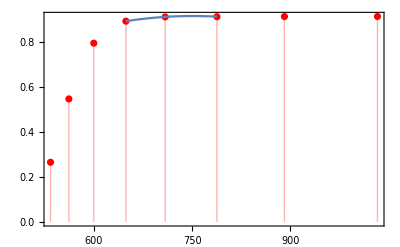

0.905107

0.9171

```mathematica
lm4 = LinearModelFit[{{649,0.89425},{709,0.91328},{788,0.91412}}, {x^2,x}, x];
Show[ListPlot[DataMax, PlotStyle -> Red,Filling->Bottom],Plot[lm4[x],{x, 649, 788}],Frame -> True]
lm4[677]
lm4[746]
```

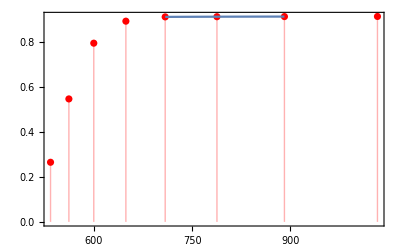

0.913717

0.91446

```mathematica
lm5 = LinearModelFit[{{709,0.91328},{788,0.91412},{891,0.91469}}, {x^2,x}, x];
Show[ListPlot[DataMax, PlotStyle -> Red,Filling->Bottom],Plot[lm5[x],{x, 709, 891}],Frame -> True]
lm5[746]
lm5[836]
```

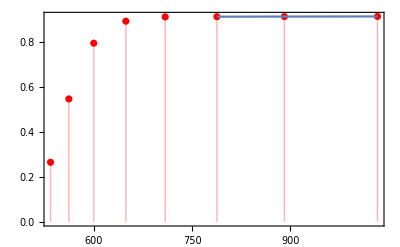

0.914404

0.914969

```mathematica
lm6 = LinearModelFit[{{788,0.91412},{891,0.91469},{1033,0.91523}}, {x^2,x}, x];
Show[ListPlot[DataMax, PlotStyle -> Red,Filling->Bottom],Plot[lm6[x],{x, 788, 1033}],Frame -> True]
lm6[836]
lm6[955]
```

## Minimum points for superior transmitances

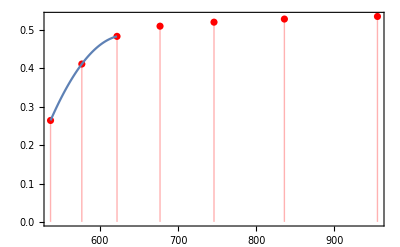

0.365507

0.46071

```mathematica
LM1 = LinearModelFit[{{537,0.26442},{577,0.41151},{622,0.48360}}, {x^2,x}, x];
Show[ListPlot[DataMin, PlotStyle -> Red,Filling->Bottom],Plot[LM1[x],{x, 537, 622}],Frame -> True]
LM1[562]
LM1[600]
```

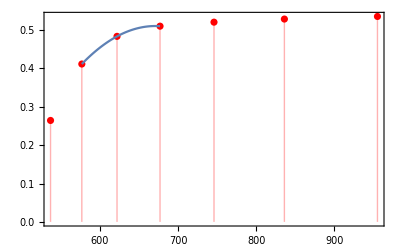

0.46071

0.479392

```mathematica
LM2 = LinearModelFit[{{577,0.41151},{622,0.48360},{677,0.51017}}, {x^2,x}, x];
Show[ListPlot[DataMin, PlotStyle -> Red,Filling->Bottom],Plot[LM2[x],{x, 577, 677}],Frame -> True]
LM2[600]
LM2[649]
```

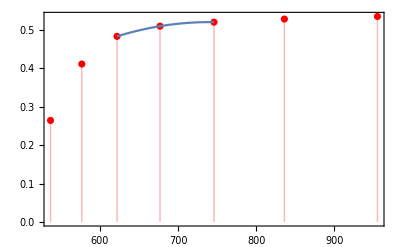

0.479392

0.342596

```mathematica
LM3 = LinearModelFit[{{622,0.48360},{677,0.51017},{746,0.52063}}, {x^2,x}, x];
Show[ListPlot[DataMin, PlotStyle -> Red,Filling->Bottom],Plot[LM3[x],{x, 622, 746}],Frame -> True]
LM3[649]
LM3[709]
```

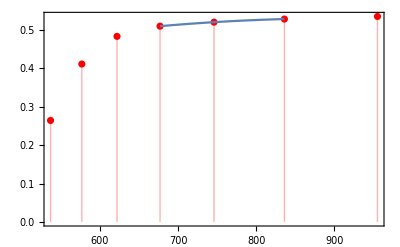

0.51548

0.525191

```mathematica
LM4 = LinearModelFit[{{677,0.51017},{746,0.52063},{836,0.52873}}, {x^2,x}, x];
Show[ListPlot[DataMin, PlotStyle -> Red,Filling->Bottom],Plot[LM4[x],{x, 677, 836}],Frame -> True]
LM4[709]
LM4[788]
```

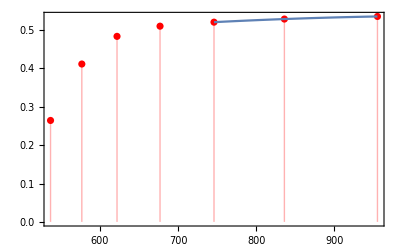

0.52473

0.532413

```mathematica
DataMin={{537,0.26442},{577,0.41151},{622,0.48360},{677,0.51017},{746,0.52063},{836,0.52873},{955,0.53549}};
LM5 = LinearModelFit[{{746,0.52063},{836,0.52873},{955,0.53549}}, {x^2,x}, x];
Show[ListPlot[DataMin, PlotStyle -> Red,Filling->Bottom],Plot[LM5[x],{x, 746, 955}],Frame -> True]
LM5[788]
LM5[891]
```